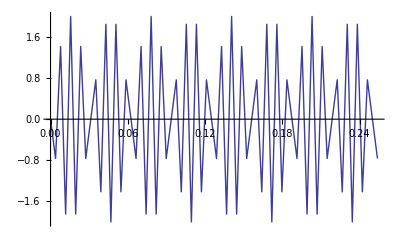

```mathematica
f[t_]:=2Sin[2π(400)t];(*4 Cos[2 π (32) t^2]+4 Cos[2 π (104 t-32 t^2)]*)
Tf=(*Import["/home/abstract/Desktop/Arra.dat","Table"];*)Table[{t,f[t]},{t,0,0.256,1/256}];
Tft=Table[Tf[[x,1]],{x,1,Length[Tf]}]//N;
Tfm=Table[Tf[[x,2]],{x,1,Length[Tf]}]//N;
ListLinePlot[Tf,PlotRange->All]
```

```mathematica
(* Lee *)
dp=Length[Tf];bw=1/(16tt);m=dp;mo=dp;
dp2=dp*2;mm=dp/128;nn=dp2/256;tin[i_]:=Tft[[i]];ain[i_]:=Tfm[[i]];
mvopt=0;as=0;nf=10;mt=10;
(***********************)
```

```mathematica
(* Cálculo del delta de t de la señal *)
(* dtcalc(dp,tin,dt) *)
dtsum=0.0;
Do[delt=tin[i+1]-tin[i];dtsum=dtsum+delt,{i,1,dp-1}]
dt=dtsum/(dp-1);
(*************************)
```

```mathematica
(* Cálcula y remueve el valor medio de la señal *)
(* mean(dp,ain) *)
asum=0.0;
Do[asum=asum+ain[i],{i,1,dp}];meanv=asum/dp;
Do[aain[i]=ain[i]-meanv,{i,1,dp}]
If[mvopt==1,
Do[ain[i]=aain[i],{i,1,dp}]];
```

```mathematica
(*******Ventana de Hamming*************)
```

```mathematica
mtime=(dp-1)*dt;del1=0.1*mtime;del2=0.9*mtime;const=π/del1;
Do[{t=(j-1)*dt,If[t≤del1,ain[j]=ain[j]*(.54-.46*Cos[const*t]),If[t≥del2&&t≤mtime,ain[j]=ain[j]*(.54-.46*Cos[const*(mtime-t)])]]},{j,1,dp}]
```

```mathematica
(*********Señal Analítica***********)
```

```mathematica
Do[{sum=0.0,
Do[{sumb=0.0,
If[i-j≠0,{n=i-j,val=π*n/2,sval=Sin[val],sumb=ain[j]*sval*sval/val}],
sum=sum+sumb},
{j,1,dp}],
s[i]=ain[i]+ⅈ sum},
{i,1,dp}];
```

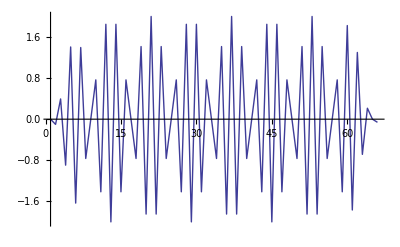

```mathematica
ListLinePlot[Table[Re@s[i],
{i,1,dp}],PlotRange->All]
```

```mathematica
(***************Wigner*******************)
```

```mathematica
(**************Ventana Gaussiana***************)
```

```mathematica
dp2=2dp;coef1000=2.0dt;df=1.0/(4.0dp dt);nf2=2nf;mt2=2mt;f1=mt;f2=nf;
val=1.0/((2π)^2 (f1 f2 df dt));
Do[q1=j;
Do[q2=i;cf=-((q1^2)/(2.0 f1^2))-((q2^2)/(2.0 f2^2));hg[i,j]=val Exp[cf],
{i,-nf2,nf2}],
{j,-mt2,mt2}];
Do[
Do[wdf[i,j]=0,
{i,1,dp}],
{j,1,dp/2}];
Do[(*5000*)
Do[(*1000*)
If[j≥i,dum=s[j-i+1],dum=0+ⅈ 0];
If[j+i-1>dp,dum4=0+ⅈ 0,dum4=s[j+i-1]];
c[i]=coef1000 dum4 Conjugate[dum];
If[i≠1&&i≠dp+1,c[dp2-i+2]=Conjugate[c[i]]],
(*1000*){i,1,dp+1}];
cc[j]=Table[c[x],{x,1,dp2}];
(****************FFT*************************)
dp2=2dp;cte=dp2;val=(Log[cte]/Log[2])+0.1//N;
Block[{j=1},
Do[(*40*)
If[i≥j,Goto["10"],
dum3=c[j];c[j]=c[i];c[i]=dum3];
Label["10"];k=dp;
Label["20"];If[k≥j,Goto["30"],
j=j-k;k=k/2];
Goto["20"];
Label["30"];j=j+k,
(*40*){i,1,dp2-1}]];
Do[(*70*)
coef=2^n;coef1=coef/2;θ=π/coef1;dum2=1+ⅈ 0;dum=Cos[θ]-ⅈ Sin[θ];
Do[(*60*)
Do[(*50*)
ii=i+coef1;dum3=c[ii]*dum2;c[ii]=c[i]-dum3;
c[i]=c[i]+dum3,
(*50*){i,j,dp2,coef}];
dum2=dum2*dum,
(*60*){j,1,coef1}],
(*70*){n,1,val}];
(************* FFT dat**************************)
ik=Mod[(j-1),mm];
If[ik==0,
Do[rc[i]=Re@c[i],{i,1,dp2,nn}]];
If[ik==0,rcc[j]=Table[rc[x],{x,1,dp2,nn}]];
(***************************************)
m1=0;
Do[(*4000*)
m1=m1+1;n1=0;
If[Abs[j-m]≤mt2,
Do[(*3000*)n1=n1+1;
Do[(*2500*)k1=kk;
If[kk<1,k1=kk+dp2];
If[kk>dp2,k1=kk-dp2];
wdf[n1,m1]=wdf[n1,m1]+Re[c[k1]]hg[kk-n,j-m]df dt,
(*2500*){kk,n-nf2,n+nf2}],
(*3000*){n,1,dp2,nn}]],
(*4000*){m,1,dp,mm}],
(*5000*){j,1,dp}]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

```mathematica
CC=Table[Re@cc[j],{j,1,dp}];
```

```mathematica
Dimensions[CC]
```

{256,512}

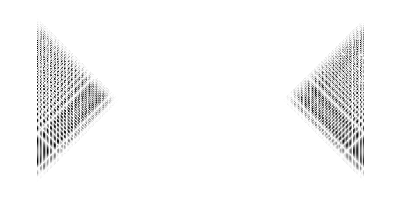

```mathematica
ArrayPlot[CC]
```

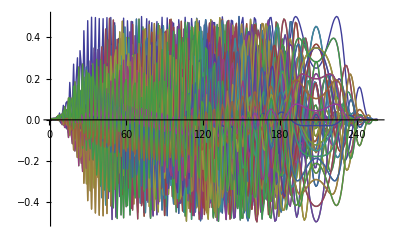

```mathematica
ListLinePlot[Transpose[CC],PlotRange->All]
```

```mathematica
WW=Table[rcc[x],{x,1,dp,nn}];
```

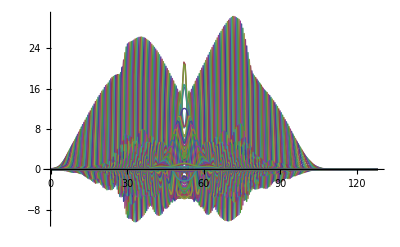

```mathematica
ListLinePlot[WW,PlotRange->All,DataRange->{0,128}]
```

```mathematica
ListContourPlot[WW,PlotRange->All,DataRange->{{0,128},{0,1}}]
```

-Graphics-

```mathematica
ListPlot3D[WW,PlotRange->All,DataRange->{{0,128},{0,1}}]
```

-Graphics3D-

```mathematica
WV=Table[wdf[j,i],{j,1,dp2/nn},{i,1,dp/mm}];
```

```mathematica
Dimensions[WV]
```

{256,128}

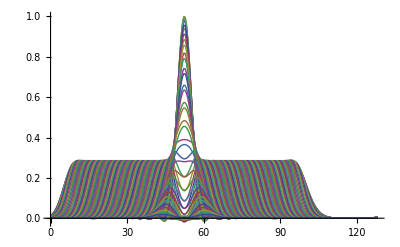

```mathematica
ListLinePlot[Transpose[WV],PlotRange->All,DataRange->{0,128}]
```

```mathematica
ListContourPlot[Transpose[WV],PlotRange->All,DataRange->{{0,128},{0,1}}]
```

-Graphics-

```mathematica
ListPlot3D[WV,PlotRange->All,DataRange->{{0,1},{0,128}}]
```

-Graphics3D-